```mathematica
ClearAll["Global`*"];
```

```mathematica
F[t_]:=HeavisideTheta[1-t]*Cos[10*t];
```

```mathematica
γ=1;ω=1;
```

```mathematica
s=NDSolve[{x''[t]==-ω^2*x[t]-γ*x'[t]+F[t],x[0]==0,x'[0]==0},x,{t,0,20}]
```

{{x→InterpolatingFunction[…]}}

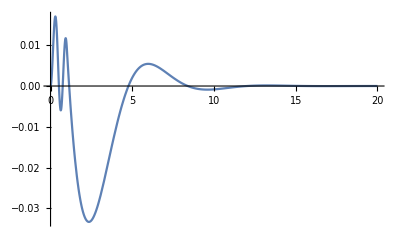

```mathematica
Plot[Evaluate[x[t]/. s],{t,0,20},PlotRange->All]
```

```mathematica
a=DSolve[{y''[t]+y'[t]+y[t]==0,y[0]==1,y'[0]==1},y[t],t]
```

{{y[t]→ⅇ^(-t/2) (Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])}}

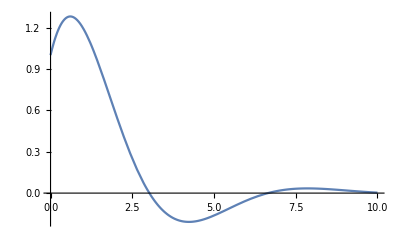

```mathematica
Plot[ⅇ^(-t/2) (Cos[(√3 t)/2]+√3 Sin[(√3 t)/2]),{t,0,10},PlotRange->All]
```